# Tarea-Examen 2 & 3

## Tarea Examen 2

Funciones

### Galerkin1D (Problema 1)

```mathematica
Galerkin1D[f_,n_,dominio_,Φ_:ϕ,b_:B]:=Module[{i,j,K,F},
	K=Table[b[i,j,dominio],{i,n},{j,n}]]ᵀ;
	F=Table[Integrate[f Φ[i],{x,dominio[[1]],dominio[[2]]}],{i,n}];
	Print[{"K="MatrixForm[K],"F="MatrixForm[F]}];
	LinearSolve[K,F].Table[Φ[i],{i,n}]
]
```

### Galerkin2D (Problema 2)

```mathematica
Galerkin2D1[f_,n_,dominio_,ϕ_,B_:B]:=Module[{i,j,K,F},
	K=Table[B[i,j,dominio],{i,n},{j,n}]ᵀ;
	F=Table[Integrate[f ϕ[[i]],{x1,dominio[[1,1]],dominio[[1,2]]},{x2,dominio[[2,1]],dominio[[2,2]]}],{i,n}];
	Print[{"K="MatrixForm[K],"F="MatrixForm[F]}];
	LinearSolve[K,F].Table[ϕ[[i]],{i,n}]
]
```

### Galerkin2D (Problema 3 & Funcional Modificado)

```mathematica
Galerkin2D2[f_,n_,dominio_,ϕ_,b_:B]:=Module[{i,j,K,F},
	K=Table[b[i,j,dominio],{i,n},{j,n}]ᵀ;
	F=Table[Integrate[f ϕ[[i]],{x2,dominio[[1,1]],dominio[[1,2]]}],{i,n}];
	Print[{"K="MatrixForm[K],"F="MatrixForm[F]}];
	LinearSolve[K,F].Table[ϕ[[i]],{i,n}]
]
```

### Base Dominio Cuadrado

```mathematica
g[dimension_,dominio_]:= Module[{variables},
	variables=Table[ToExpression["x"<>ToString[i]],{i,dimension}];
	Product[(variables[[i]]^2-dominio[[i]]^2),{i,dimension}]
]
```

```mathematica
GeneradorVectorAlfa[dimension_,orden_]:=Module[{x,y,i,j,A1,A2,A3},
	A1=Table[Reduce[Sum[ToExpression["α"<>ToString[i]],{i,dimension}]==j,Table[ToExpression["α"<>ToString[i]],{i,dimension}],Integers],{j,orden}];
	For[j=1,j<dimension,j++,
		A1=Table[A1/.{C[j]-> i},{i,0,orden}]
	];
	A1= Flatten[A1];
	A2=Flatten[Table[FindInstance[A1[[i]],Table[ToExpression["α"<>ToString[i]],{i,dimension}]],{i,Dimensions[A1][[1]]}],1];
	A3=Table[Table[ToExpression["α"<>ToString[i]],{i,dimension}]/.A2[[i]],{i,Dimensions[A2][[1]]}];
	A3=Select[A3,#[[dimension]]>=0&];
	A3=Flatten[Table[Select[A3,Total[#]==i&],{i,0,orden}],1]
]
```

```mathematica
BaseHiperCubica[dimension_,orden_,dominio_]:=Module[{variables,funcionbase,alfa},
	variables=Table[ToExpression["x"<>ToString[i]],{i,dimension}];
	alfa=GeneradorVectorAlfa[dimension,orden];
	funcionbase=g[dimension,dominio];
	Join[{funcionbase},Table[Product[variables[[i]]^alfa[[j,i]],{i,dimension}] funcionbase,{j,Dimensions[alfa][[1]]}]]
]
```

### Base Serie de Potencias 2D

```mathematica
Base2D[dimension_,orden_,offset_:0]:=Module[{variables,funcionbase,alfa},
	variables=Table[ToExpression["x"<>ToString[i]],{i,dimension}];
	alfa=GeneradorVectorAlfa[dimension,orden];
	Table[Product[(variables[[i]]^alfa[[j,i]]+offset),{i,dimension}] ,{j,Dimensions[alfa][[1]]}]
]
```

Ejemplo

### Base Propuesta

```mathematica
ϕ[i_]:= x^i
```

### Forma Bilineal

```mathematica
B[i_,j_,dominio_]:=Integrate[D[ϕ[i],x]D[ϕ[j],x],{x,dominio[[1]],dominio[[2]]}]
```

### Solucion

```mathematica
u=Galerkin1D[Sin[(Pi x)/2],2,{0,1},ϕ,B]
```

{K= (1 | 1
1 | 4/3),F= (4/π^2
(8 (-2+π))/π^3)}

-(8 (-6+π) x)/π^3+(12 (-4+π) x^2)/π^3

### Visualizacion

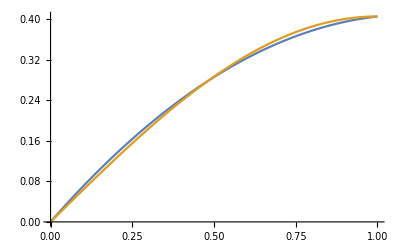

```mathematica
f=y[x]/.DSolve[{y''[x]==-Sin[(Pi x)/2],y[0]==0,y'[1]==0},y[x],x];
Plot[{u,f},{x,0,1}]
```

Ejercicios

### Primer Problema

#### Base Propuesta

```mathematica
ψ[i_]:= x^i(x-1)
```

#### Forma Bilineal

```mathematica
Bi1[i_,j_,dominio_]:=-Integrate[D[ψ[i],x]D[ψ[j],x],{x,dominio[[1]],dominio[[2]]}]-Integrate[ψ[i]ψ[j],{x,dominio[[1]],dominio[[2]]}]
```

#### Solucion (2 Dimensiones)

```mathematica
u1=Galerkin1D[x,2,{0,1},ψ,Bi1];
```

{K= (-11/30 | -11/60
-11/60 | -1/7),F= (-1/12
-1/20)}

{(ⅇ^-x (-ⅇ+ⅇ^(1+2 x)+ⅇ^x x-ⅇ^(2+x) x))/(-1+ⅇ^2)}

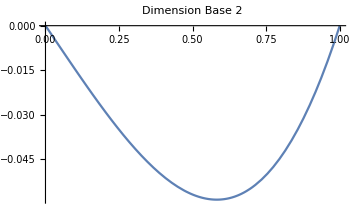
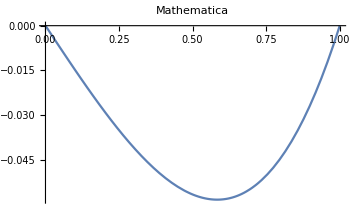

```mathematica
f=y[x]/.DSolve[{y''[x]-y[x]==x,y[0]==0,y[1]==0},y[x],x]
{Plot[u1,{x,0,1},ImageSize->Medium,PlotLabel->"Dimension Base "<>ToString[2] ,LabelStyle->Directive[Bold,12]],Plot[f,{x,0,1},ImageSize->Medium,PlotLabel->"Mathematica",LabelStyle->Directive[Bold,12]]}
```

#### Solucion (3 Dimensiones)

```mathematica
u2=Galerkin1D[x,3,{0,1},ψ,Bi1];
```

{K= (-11/30 | -11/60 | -23/210
-11/60 | -1/7 | -89/840
-23/210 | -89/840 | -113/1260),F= (-1/12
-1/20
-1/30)}

{(ⅇ^-x (-ⅇ+ⅇ^(1+2 x)+ⅇ^x x-ⅇ^(2+x) x))/(-1+ⅇ^2)}

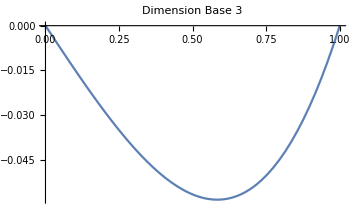
{-Graphics-,-Graphics-}

```mathematica
f=y[x]/.DSolve[{y''[x]-y[x]==x,y[0]==0,y[1]==0},y[x],x]
{Plot[u2,{x,0,1},ImageSize->Medium,PlotLabel->"Dimension Base "<>ToString[3] ,LabelStyle->Directive[Bold,12]],Plot[f,{x,0,1},ImageSize->Medium,PlotLabel->"Mathematica",LabelStyle->Directive[Bold,12]]}
```

#### Visualizacion Examen

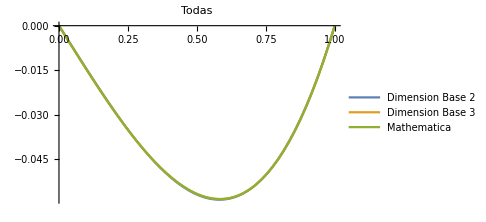

```mathematica
Plot[{u1,u2,f(1.)},{x,0,1},ImageSize->Medium,PlotLegends->{"Dimension Base 2","Dimension Base 3","Mathematica"},PlotLegends->"All Expressions",PlotLabel->"Todas",LabelStyle->Directive[Bold,12]]
```

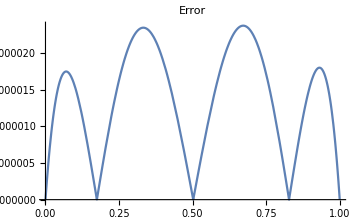
{-Graphics-,-Graphics-}

```mathematica
f=y[x]/.DSolve[{y''[x]-y[x]==x,y[0]==0,y[1]==0},y[x],x];
{Plot[u2,{x,0,1},ImageSize->Medium,PlotLabel->"Dimension Base "<>ToString[3] ,LabelStyle->Directive[Bold,12]],Plot[Abs[f-u2],{x,0,1},ImageSize->Medium,PlotLabel->"Error",LabelStyle->Directive[Bold,12]]}
```

{(ⅇ^-x (-ⅇ+ⅇ^(1+2 x)+ⅇ^x x-ⅇ^(2+x) x))/(-1+ⅇ^2)}

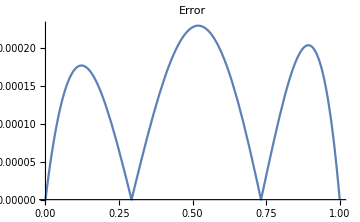
{-Graphics-,-Graphics-}

```mathematica
f=y[x]/.DSolve[{y''[x]-y[x]==x,y[0]==0,y[1]==0},y[x],x]
{Plot[u1,{x,0,1},ImageSize->Medium,PlotLabel->"Dimension Base "<>ToString[2] ,LabelStyle->Directive[Bold,12]],Plot[Abs[f-u1],{x,0,1},ImageSize->Medium,PlotLabel->"Error",LabelStyle->Directive[Bold,12]]}
```

### Segundo Problema

#### Base Propuesta

```mathematica
BaseRectangular=BaseHiperCubica[2,3,{3,2}];
n=Length[BaseRectangular];
```

#### Forma Bilineal

```mathematica
Bi2[i_,j_,dominio_]:=-Integrate[D[BaseRectangular[[i]],x1]D[BaseRectangular[[j]],x1]+D[BaseRectangular[[i]],x2]D[BaseRectangular[[j]],x2],{x1,dominio[[1,1]],dominio[[1,2]]},{x2,dominio[[2,1]],dominio[[2,2]]}]
```

#### Solucion (5 Dimensiones)

```mathematica
SolucionMathematica2=NDSolveValue[{∇_{x,y}^2 U[x,y] ==- 2, 
  DirichletCondition[U[x, y] == 0, True]}, U, {x, -3,3},{y,-2,2}];
```

```mathematica
U22D=Galerkin2D1[-2,5,{{-3,3},{-2,2}},BaseRectangular,Bi2];
```

{K= (-39936/5 | 0 | 0 | -1019904/175 | 0
0 | -2568192/175 | 0 | 0 | 0
0 | 0 | -3566592/175 | 0 | 0
-1019904/175 | 0 | 0 | -5193728/175 | 0
0 | 0 | 0 | 0 | -4313088/175),F= (-768
0
0
-3072/5
0)}

```mathematica
SolucionMathematica2=NDSolveValue[{∇_{x,y}^2 U[x,y] ==- 2, 
  DirichletCondition[U[x, y] == 0, True]}, U, {x, -3,3},{y,-2,2}];
{Plot3D[U22D,{x1,-3,3},{x2,-2,2},ImageSize->Medium],Plot3D[SolucionMathematica2[x,y],{x, -3,3},{y,-2,2},ImageSize->Medium]}
```

{-Graphics3D-,-Graphics3D-}

#### Error

```mathematica
MatrixForm[{{Plot3D[{U22D,SolucionMathematica2[x1,x2]},{x1,-3,3},{x2,-2,2},ImageSize->Medium],Plot3D[Abs[SolucionMathematica2[x1,x2]-U22D],{x1,-3,3},{x2,-2,2},ImageSize->Medium]},{Manipulate[Abs[SolucionMathematica2[x1,x2]-U22D]/.{x1->x,x2->y},Style["Error",Bold,Medium],{x,-3,3},{y,-2,2}]}}]
```

({-Graphics3D-,-Graphics3D-}
{})

#### Visualizacion Examen

```mathematica
MatrixForm[{{Plot3D[U22D,{x1,-3,3},{x2,-2,2},ImageSize->Medium,PlotLabel->"Gallarkin",LabelStyle->Directive[Bold,12]],Plot3D[SolucionMathematica2[x,y],{x, -3,3},{y,-2,2},ImageSize->Medium,PlotLabel->"Mathematica",LabelStyle->Directive[Bold,12]]},{Plot3D[{U22D,SolucionMathematica2[x1,x2]},{x1,-3,3},{x2,-2,2},ImageSize->Medium,PlotLabel->"Ambas",LabelStyle->Directive[Bold,12]],Plot3D[Abs[U22D-SolucionMathematica2[x1,x2]],{x1,-3,3},{x2,-2,2},ImageSize->Medium,PlotLabel->"Error",LabelStyle->Directive[Bold,12]]}}]
```

(-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-)

### Tercer Problema

#### Base Propuesta

```mathematica
(*BaseTercerProblema[n_]:=Table[Cos[(Pi x2)/2.](x1^i+1.),{i,0,n-1}]*)
(*BaseTercerProblema[n_]:=Table[(x1^i+1.)(x2^2-1.),{i,0,n-1}];*)
BaseTercera=Join[{1},Base2D[2,2,0]];
BaseTercera=Table[BaseTercera[[i]](x2^2-1.),{i,Length[BaseTercera]}];
(*BaseTercera=Table[BaseTercera[[i]]Cos[(Pi x2)/2.],{i,Length[BaseTercera]}]*)
(*BaseTercera=Table[BaseTercera[[i]]Cos[(Pi x2)/2.],{i,Length[BaseTercera]}]*)
(*BaseTercera=BaseTercerProblema[5]*)
n=Length[BaseTercera];
```

#### Forma Bilineal

```mathematica
Bi3[i_,j_,dominio_]:=Integrate[D[BaseTercera[[i]],x1]D[BaseTercera[[j]],x1]+D[BaseTercera[[i]],x2]D[BaseTercera[[j]],x2]+BaseTercera[[i]]BaseTercera[[j]],{x1,dominio[[1,1]],dominio[[1,2]]},{x2,dominio[[2,1]],dominio[[2,2]]}]
```

#### Solucion (5 Dimensiones)

```mathematica
U32D=Galerkin2D2[-2Cos[(Pi x2)/2],n,{{-1.,1.},{-1.,1.}},BaseTercera,Bi3];
```

{K= (7.46667 | 0 | 0. | 1.37143 | 0 | 2.48889
0 | 3.50476 | 0 | 0 | 0. | 0
0. | 0 | 4.62222 | 0. | 0 | 0.
1.37143 | 0 | 0. | 1.77778 | 0 | 0.457143
0 | 0. | 0 | 0 | 1.47302 | 0
2.48889 | 0 | 0. | 0.457143 | 0 | 4.33778),F= (2.0641
0.
2.0641 x1
0.281921
0.
2.0641 x1^2)}

```mathematica
SolucionMathematica3=NDSolveValue[{∇_{x1,x2}^2 U[x1,x2]==NeumannValue[Cos[(Pi x2)/2],x1==-1||x1==1], U[x1,1]==0,U[x1,-1]==0},U, {x1, -1,1},{x2,-1,1}];
```

```mathematica
{Plot3D[{U32D},{x1,-1,1},{x2,-1,1},ImageSize->Medium,PlotLabel->"Gallarkin",LabelStyle->Directive[Bold,12]],Plot3D[{SolucionMathematica3[x1,x2]},{x1,-1,1},{x2,-1,1},ImageSize->Medium,PlotLabel->"Mathematica",LabelStyle->Directive[Bold,12]]}
```

{-Graphics3D-,-Graphics3D-}

#### Error

```mathematica
MatrixForm[{{Plot3D[{U32D,SolucionMathematica3[x1,x2]},{x1,-1,1},{x2,-1,1},ImageSize->Medium,PlotLabel->"Ambas",LabelStyle->Directive[Bold,12]],Plot3D[{Abs[U32D-SolucionMathematica3[x1,x2]]},{x1,-1,1},{x2,-1,1},ImageSize->Medium,PlotLabel->"Error",LabelStyle->Directive[Bold,12]]},{Manipulate[Abs[SolucionMathematica2[x1,x2]-U22D]/.{x1->x,x2->y},Style["Error",Bold,Medium],{x,-3,3},{y,-2,2}]}}]
```

({-Graphics3D-,-Graphics3D-}
{})

#### Visualizacion Examen

```mathematica
MatrixForm[{{Plot3D[{U32D},{x1,-1,1},{x2,-1,1},ImageSize->Medium,PlotLabel->"Gallarkin",LabelStyle->Directive[Bold,12]],Plot3D[{SolucionMathematica3[x1,x2]},{x1,-1,1},{x2,-1,1},ImageSize->Medium,PlotLabel->"Mathematica",LabelStyle->Directive[Bold,12]]},{Plot3D[{U32D,SolucionMathematica3[x1,x2]},{x1,-1,1},{x2,-1,1},ImageSize->Medium,PlotLabel->"Ambas",LabelStyle->Directive[Bold,12]],Plot3D[{Abs[U32D-SolucionMathematica3[x1,x2]]},{x1,-1,1},{x2,-1,1},ImageSize->Medium,PlotLabel->"Error",LabelStyle->Directive[Bold,12]]}}]
```

(-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-)

## Tarea Examen 3

Funciones

### Base Local

```mathematica
BaseLocal[orden_]:=Module[{i,j,steplocal=2/orden,histograma,puntos=Table[1,orden+1]},
	histograma=Table[Table[{-1+steplocal i,puntos[[j]]KroneckerDelta[i,j-1] },{i,0,orden}],{j,orden+1}];
	Table[InterpolatingPolynomial[histograma[[i]],ζ],{i,orden+1}]
]
```

### Nodos Globales

```mathematica
NodosGlobales[dominio_,subdominios_,orden_]:=Module[{stepglobal=(dominio[[2]]-dominio[[1]])/subdominios},
	Table[Table[dominio[[1]]+stepglobal i+(j stepglobal)/orden,{j,0,orden}],{i,0,subdominios-1}]
]
```

```mathematica
{dominio,subdominios,orden}={{0,1},4,1};
nodosglobales=NodosGlobales[dominio,subdominios,orden]
```

{{0,1/4},{1/4,1/2},{1/2,3/4},{3/4,1}}

```mathematica
Table[Sum[dominio[[1]]+(i+j-1) stepglobal<x<dominio[[1]]+(i+j) stepglobal,{i,orden+1}],{j,0,(subdominios-2)}]
```

{(0<x<stepglobal)+(stepglobal<x<2 stepglobal),(stepglobal<x<2 stepglobal)+(2 stepglobal<x<3 stepglobal),(2 stepglobal<x<3 stepglobal)+(3 stepglobal<x<4 stepglobal)}

```mathematica
stepglobal=nodosglobales[[1,2]]-nodosglobales[[1,1]];
nodosglobales=NodosGlobales[dominio,subdominios,orden];
```

### Mapeo Local-Global

```mathematica
MapeoLocalGlobal[dominio_,subdominios_,orden_]:=Module[{MapeoLocalGlobal,nodosglobales,stepglobal,baselocal},
	baselocal=BaseLocal[orden];
	nodosglobales=NodosGlobales[dominio,subdominios,orden];
	stepglobal=nodosglobales[[1,-1]]-nodosglobales[[1,1]];
	Table[Table[FullSimplify[baselocal[[i]]/.ζ-> (2(x-((nodosglobales[[j,1]]+nodosglobales[[j,-1]])/2)))/stepglobal],{i,orden+1}],{j,subdominios}]
]
```

### Base Global

```mathematica
BaseGlobal[dominio_,subdominios_,orden_]:=Module[{base,nodosglobales,stepglobal,baseglobal,i,j},
	base=MapeoLocalGlobal[dominio,subdominios,orden];
	nodosglobales=NodosGlobales[dominio,subdominios,orden];
	baseglobal=Table[0,(subdominios-1)+(orden-1)subdominios];
	For[i=1,i<subdominios+1,i++,
		For[j=2,j<(orden+1)+1,j++,
			If[j<orden+1,
				(*Casos en medio*)
				baseglobal[[(orden+1)(i-1)+j+1-i-1]]=Piecewise[{{base[[i,j]],nodosglobales[[i,1]]<x<nodosglobales[[i,-1]]}},0];
				,
				(*Ultimo caso de cada subdominio*)
				If[i+1<subdominios+1,
					baseglobal[[(orden+1)(i-1)+orden+1-i]]=Piecewise[{{base[[i,orden+1]],nodosglobales[[i,1]]<x<nodosglobales[[i,-1]]}},0]+Piecewise[{{base[[i+1,1]],nodosglobales[[i+1,1]]<x<nodosglobales[[i+1,-1]]}},0];
				];
			];
		];
	];
	baseglobal
]
```

### Sistemas Locales

```mathematica
SistemasLocales[f_,n_,dominio_,subdominioactual_,base_,bilineal_:Bilineal]:=Module[{i,j,K,F,AllK,AllF},
	K=Transpose[Table[bilineal[i,j,dominio,subdominioactual,base],{i,n},{j,n}]];
	F=Table[FullSimplify[Integrate[f base[[subdominioactual,i]],{x,dominio[[1]],dominio[[2]]}]],{i,n}];
	{K,F}
]
```

### Sistema Global

```mathematica
SistemaGlobal[f_,orden_,subdominios_,dominio_,bilineal_:Bilineal,imprimir_:1]:=Module[{i,j,k,AllK,AllF,stepglobal,nodosglobales,K,F,i0,j0,base},
	nodosglobales=NodosGlobales[dominio,subdominios,orden];
	stepglobal=nodosglobales[[1,-1]]-nodosglobales[[1,1]];
	base=MapeoLocalGlobal[dominio,subdominios,orden];
	AllK=Table[ToExpression["K"<>ToString[i]],{i,subdominios}];
	AllF=Table[ToExpression["F"<>ToString[i]],{i,subdominios}];
	K=Table[0,(subdominios-1)+(orden-1)subdominios+2,(subdominios-1)+(orden-1)subdominios+2];
	F=Table[0,(subdominios-1)+(orden-1)subdominios+2];
	
	For[i=1,i<subdominios+1,i++,
		{AllK[[i]],AllF[[i]]}=SistemasLocales[f,orden+1,{stepglobal (i-1),stepglobal i},i,base,bilineal]
	];
	
	If[imprimir==1,
	Print[{MatrixForm[Table["K"<>ToString[i]<>" ="MatrixForm[AllK[[i]]],{i,subdominios}]],MatrixForm[Table["F"<>ToString[i]<>" ="MatrixForm[AllF[[i]]],{i,subdominios}]]}];
	];
	
	For[k=0,k<subdominios,k++,
		i0=j0=k*orden;
		For[i=1,i<(orden+1)+1,i++,
			For[j=1,j<(orden+1)+1,j++,
				K[[i+i0,j+j0]]=K[[i+i0,j+j0]]+AllK[[k+1,i,j]];
			];
		];
	];
	
	For[k=0,k<subdominios,k++,
		i0=k*orden;
		For[i=1,i<(orden+1)+1,i++,
			F[[i+i0]]=F[[i+i0]]+AllF[[k+1,i]];
		];
	];

	{K,F}={Take[K,{2,-2},{2,-2}],Take[F,{2,-2}]};
	
	If[imprimir==1,
		Print[{"K ="MatrixForm[K],"F ="MatrixForm[F]}];
	];
	
	{K,F}
]
```

### Elemento Finito

```mathematica
ElementoFinitoDirichlet1D[f_,orden_,subdominios_,dominio_,bilineal_:Bilineal,imprimir_:1]:=Module[{K,F,base},
	{K,F}=SistemaGlobal[f,orden,subdominios,dominio,bilineal,imprimir];
	LinearSolve[K,F].BaseGlobal[dominio,subdominios,orden]
]
```

Ejemplo

### Forma Bilineal

```mathematica
Bilineal[i_,j_,dominio_,subdominioactual_,base_]:=Integrate[D[base[[subdominioactual,i]],x]D[base[[subdominioactual,j]],x],{x,dominio[[1]],dominio[[2]]}]+Integrate[base[[subdominioactual,i]]base[[subdominioactual,j]],{x,dominio[[1]],dominio[[2]]}]
```

### Solucion

```mathematica
u=ElementoFinitoDirichlet1D[x,2,4,{0,1},Bilineal];
```

{(K1 = (281/30 | -213/20 | 53/40
-213/20 | 322/15 | -213/20
53/40 | -213/20 | 281/30)
K2 = (281/30 | -213/20 | 53/40
-213/20 | 322/15 | -213/20
53/40 | -213/20 | 281/30)
K3 = (281/30 | -213/20 | 53/40
-213/20 | 322/15 | -213/20
53/40 | -213/20 | 281/30)
K4 = (281/30 | -213/20 | 53/40
-213/20 | 322/15 | -213/20
53/40 | -213/20 | 281/30)),(F1 = (0
1/48
1/96)
F2 = (1/96
1/16
1/48)
F3 = (1/48
5/48
1/32)
F4 = (1/32
7/48
1/24))}

{K = (322/15 | -213/20 | 0 | 0 | 0 | 0 | 0
-213/20 | 281/15 | -213/20 | 53/40 | 0 | 0 | 0
0 | -213/20 | 322/15 | -213/20 | 0 | 0 | 0
0 | 53/40 | -213/20 | 281/15 | -213/20 | 53/40 | 0
0 | 0 | 0 | -213/20 | 322/15 | -213/20 | 0
0 | 0 | 0 | 53/40 | -213/20 | 281/15 | -213/20
0 | 0 | 0 | 0 | 0 | -213/20 | 322/15),F = (1/48
1/48
1/16
1/24
5/48
1/16
7/48)}

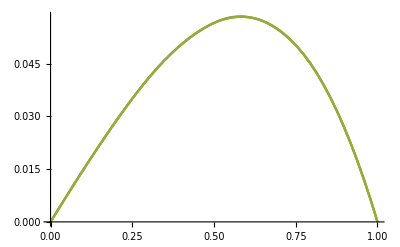

```mathematica
f=y[x]/.NDSolve[{-y''[x]+y[x]==x,y[0]==0,y[1]==0},y[x],x];
Plot[{u,f,x-(2 ⅇ Sinh[x])/(-1+ⅇ^2)},{x,0,1}]
```

Ejercicios

### Primer Problema

#### Forma Bilineal

```mathematica
Bilineal1[i_,j_,dominio_,subdominioactual_,base_]:=Integrate[D[base[[subdominioactual,i]],x]D[base[[subdominioactual,j]],x],{x,dominio[[1]],dominio[[2]]}]
```

#### Solucion

```mathematica
u=Table[ElementoFinitoDirichlet1D[Cos[Pi x],1,i+1,{0,1},Bilineal1,0],{i,9}];
f=y[x]/.DSolve[{-y''[x]==Cos[Pi x],y[0]==0,y[1]==0},y[x],x];
```

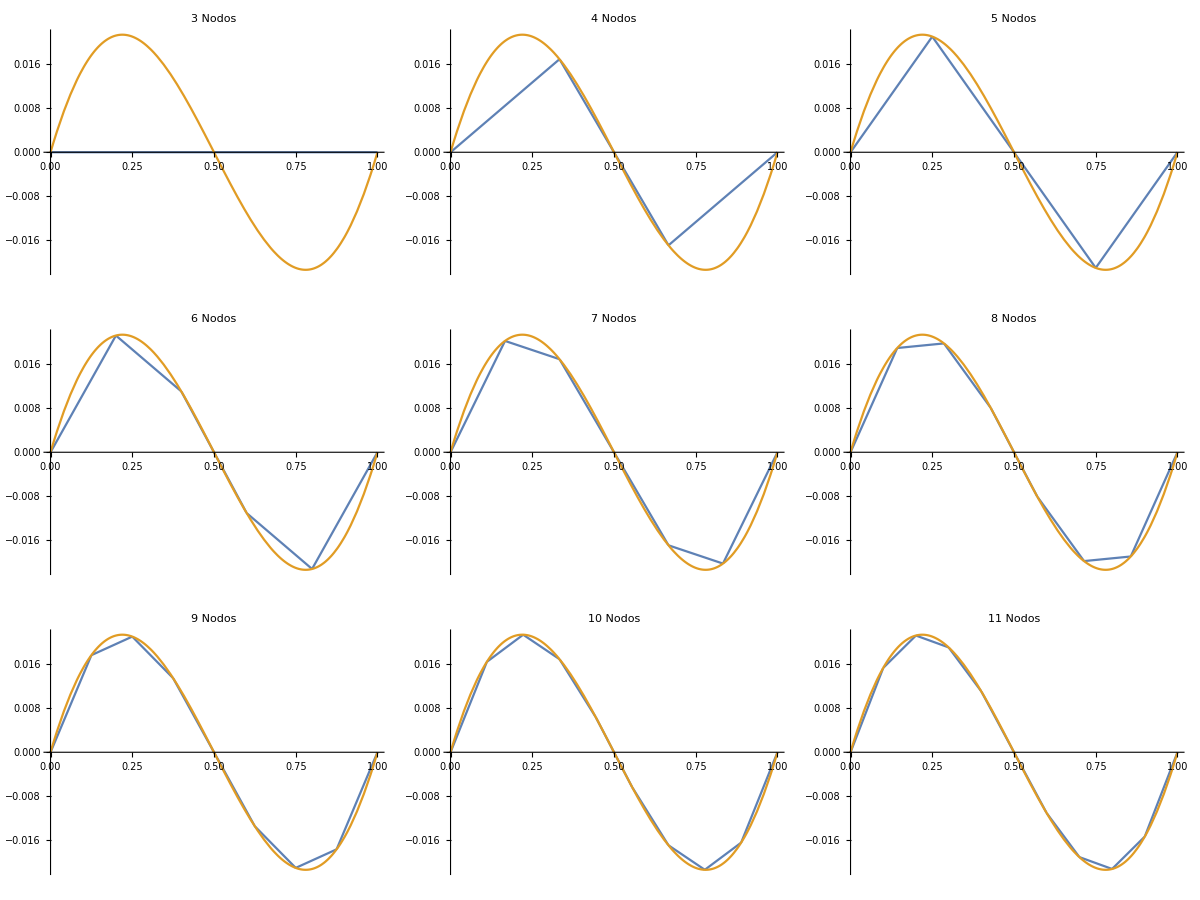
(-Graphics-)

```mathematica
MatrixForm[Partition[Table[Plot[{u[[i]],f},{x,0,1},PlotLabel->ToString[i+2]<>" Nodos"],{i,9}],3]]
```

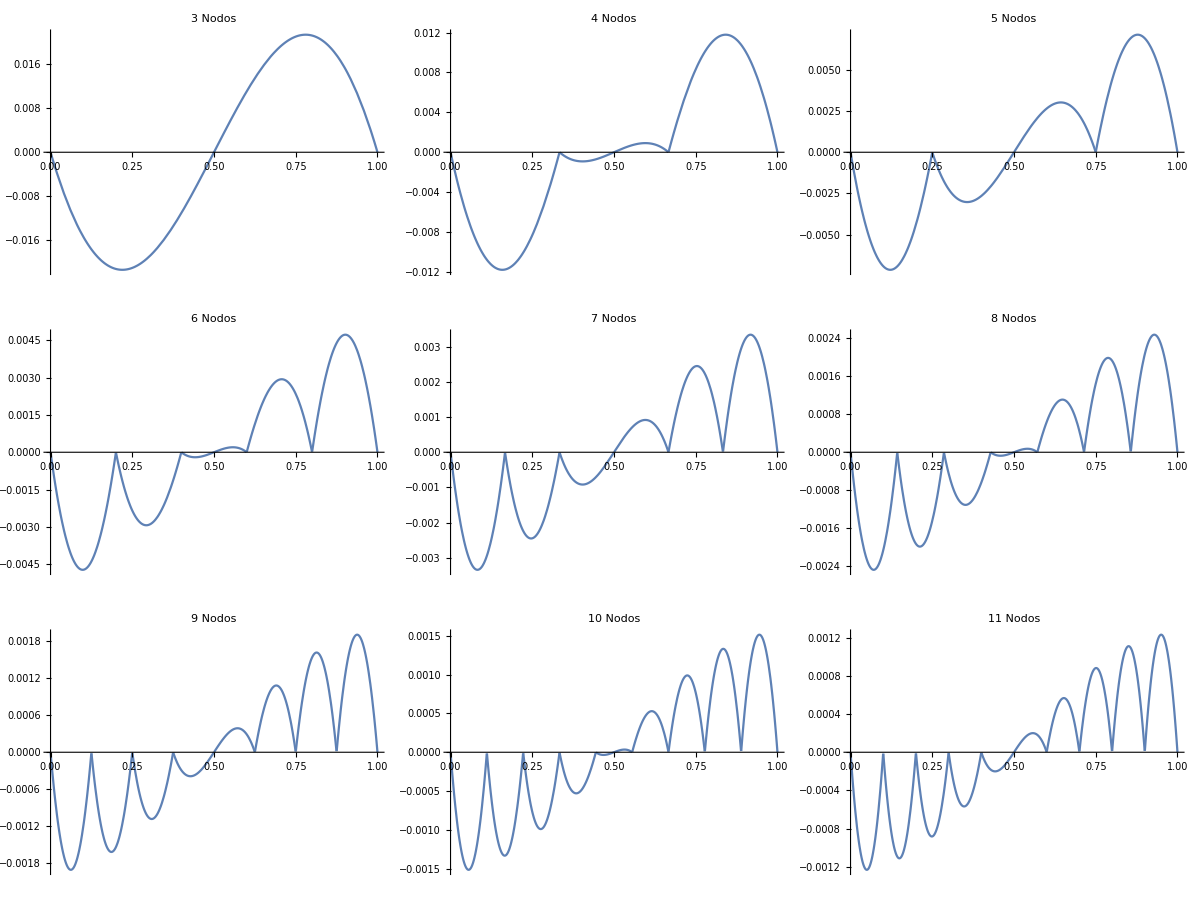
(-Graphics-)

```mathematica
MatrixForm[Partition[Table[Plot[{u[[i]]-f},{x,0,1},PlotLabel->ToString[i+2]<>" Nodos"],{i,9}],3]]
```

#### Visualizacion Examen

{(Piecewise[{{2-4 x, 1/4<x<1/2}, {0, True}}])+(Piecewise[{{4 x, 0<x<1/4}, {0, True}}]),(Piecewise[{{3-4 x, 1/2<x<3/4}, {0, True}}])+(Piecewise[{{-1+4 x, 1/4<x<1/2}, {0, True}}]),(Piecewise[{{4-4 x, 3/4<x<1}, {0, True}}])+(Piecewise[{{-2+4 x, 1/2<x<3/4}, {0, True}}])}

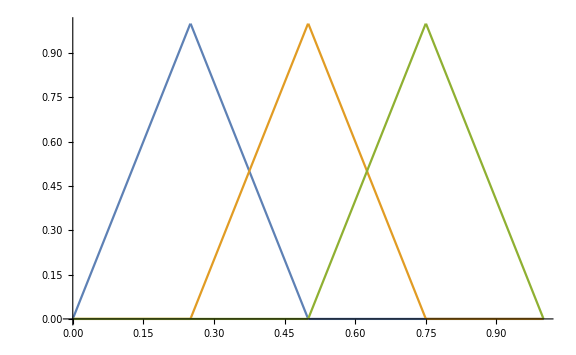

```mathematica
A=BaseGlobal[{0,1},4,1]
{Plot[A,{x,0,1},ImageSize->Large]}
```

```mathematica
u=ElementoFinitoDirichlet1D[Cos[Pi x],1,4,{0,1}];
```

{(K1 = (49/12 | -95/24
-95/24 | 49/12)
K2 = (49/12 | -95/24
-95/24 | 49/12)
K3 = (49/12 | -95/24
-95/24 | 49/12)
K4 = (49/12 | -95/24
-95/24 | 49/12)),(F1 = ((4-2 √2)/π^2
(-8+4 √2+√2 π)/(2 π^2))
F2 = (-(-4+π)/(√2 π^2)
(-2 √2+π)/π^2)
F3 = ((2 √2-π)/π^2
(-4+π)/(√2 π^2))
F4 = (-(-8+4 √2+√2 π)/(2 π^2)
(2 (-2+√2))/π^2))}

{K = (49/6 | -95/24 | 0
-95/24 | 49/6 | -95/24
0 | -95/24 | 49/6),F = (-(-4+π)/(√2 π^2)+(-8+4 √2+√2 π)/(2 π^2)
(2 √2-π)/π^2+(-2 √2+π)/π^2
(-4+π)/(√2 π^2)-(-8+4 √2+√2 π)/(2 π^2))}

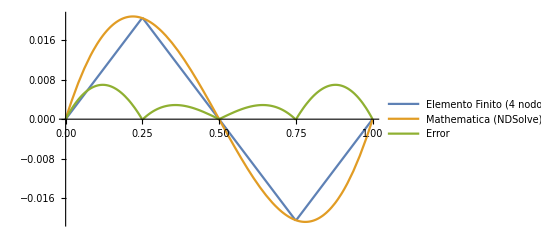

```mathematica
f=y[x]/.NDSolve[{-y''[x]+y[x]==Cos[Pi x],y[0]==0,y[1]==0},y[x],x];
Plot[{u,f(1.),Abs[u-f(1.)]},{x,0,1},PlotLegends->{"Elemento Finito (4 nodos)", "Mathematica (NDSolve)", "Error"}]
```

```mathematica
u=Table[ElementoFinitoDirichlet1D[Cos[Pi x],1,i+1,{0,1},Bilineal1,0],{i,9}];
f=y[x]/.DSolve[{-y''[x]==Cos[Pi x],y[0]==0,y[1]==0},y[x],x];
```

```mathematica
MatrixForm[Partition[Table[Plot[{u[[i]],f},{x,0,1},PlotLabel->ToString[i+2]<>" Nodos"],{i,9}],3]]
```

(-Graphics-)

### Segundo Problema

#### Forma Bilineal

```mathematica
Bilineal2[i_,j_,dominio_,subdominioactual_,base_]:=Integrate[D[base[[subdominioactual,i]],x]D[base[[subdominioactual,j]],x]-base[[subdominioactual,i]] base[[subdominioactual,j]],{x,dominio[[1]],dominio[[2]]}]
```

#### Solucion

```mathematica
u=Table[ElementoFinitoDirichlet1D[-x^2,2,i,{0,1},Bilineal2,0],{i,6}];
f=y[x]/.DSolve[{-y''[x]-y[x]==-x^2,y[0]==0,y[1]==0},y[x],x];
```

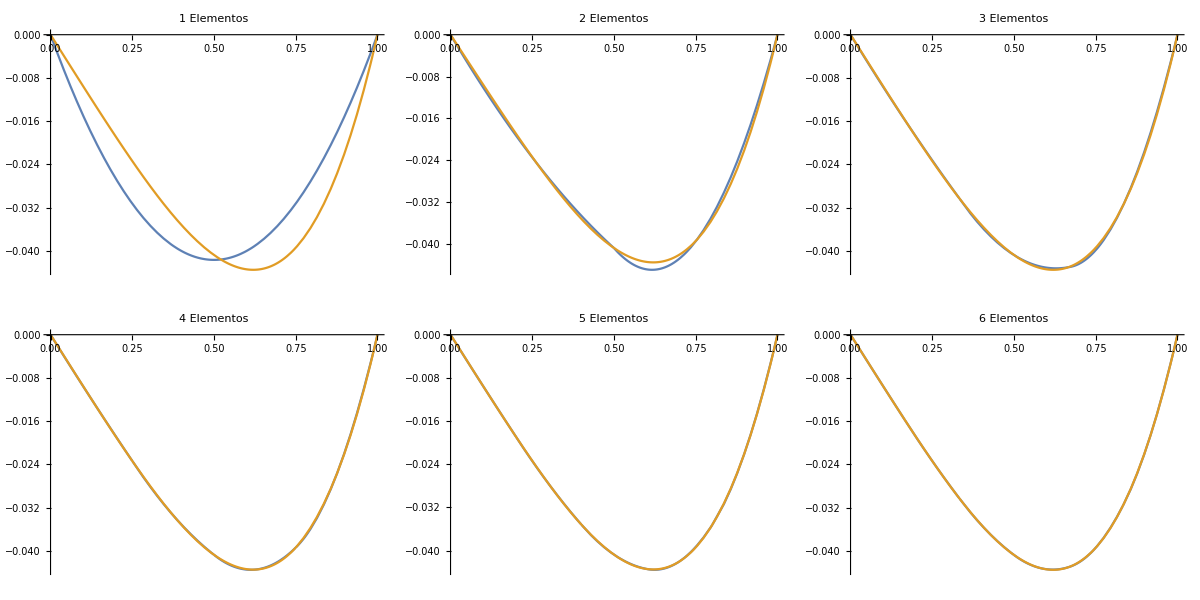
(-Graphics-)

```mathematica
MatrixForm[Partition[Table[Plot[{u[[i]],f},{x,0,1},PlotLabel->ToString[i]<>" Elementos"],{i,6}],3]]
```

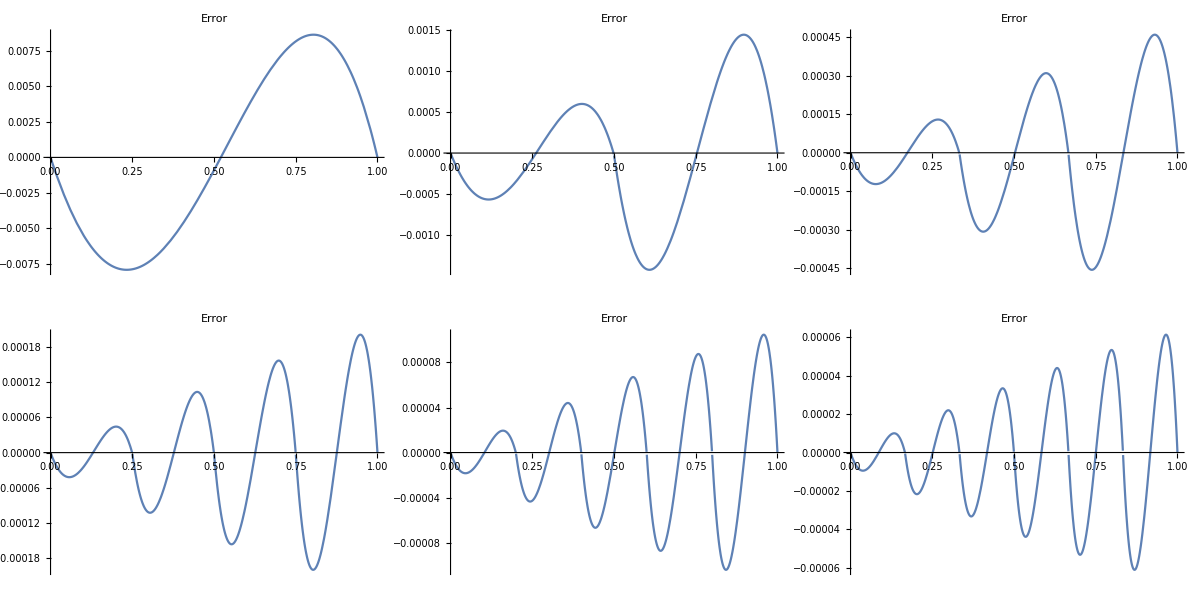
(-Graphics-)

```mathematica
MatrixForm[Partition[Table[Plot[{u[[i]]-f},{x,0,1},PlotLabel->"Error"],{i,6}],3]]
```

#### Visualizacion Examen

{Piecewise[{{16 (1-4 x) x, 0<x<1/4}, {0, True}}],(Piecewise[{{4 x (-1+8 x), 0<x<1/4}, {0, True}}])+(Piecewise[{{6+4 x (-7+8 x), 1/4<x<1/2}, {0, True}}]),Piecewise[{{-8 (1-6 x+8 x^2), 1/4<x<1/2}, {0, True}}],(Piecewise[{{(-3+4 x) (-5+8 x), 1/2<x<3/4}, {0, True}}])+(Piecewise[{{(-1+4 x) (-3+8 x), 1/4<x<1/2}, {0, True}}]),Piecewise[{{-8 (-1+2 x) (-3+4 x), 1/2<x<3/4}, {0, True}}],(Piecewise[{{4 (-1+x) (-7+8 x), 3/4<x<1}, {0, True}}])+(Piecewise[{{2 (-1+2 x) (-5+8 x), 1/2<x<3/4}, {0, True}}]),Piecewise[{{-16 (-1+x) (-3+4 x), 3/4<x<1}, {0, True}}]}

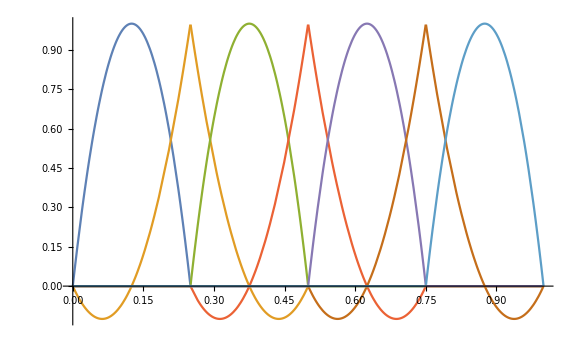

```mathematica
A=BaseGlobal[{0,1},4,2]
{Plot[A,{x,0,1},ImageSize->Large]}
```

```mathematica
u=ElementoFinitoDirichlet1D[-x^2,2,4,{0,1},Bilineal2,1];
f=y[x]/.DSolve[{-y''[x]-y[x]==-x^2,y[0]==0,y[1]==0},y[x],x]
```

{(K1 = (93/10 | -641/60 | 161/120
-641/60 | 106/5 | -641/60
161/120 | -641/60 | 93/10)
K2 = (93/10 | -641/60 | 161/120
-641/60 | 106/5 | -641/60
161/120 | -641/60 | 93/10)
K3 = (93/10 | -641/60 | 161/120
-641/60 | 106/5 | -641/60
161/120 | -641/60 | 93/10)
K4 = (93/10 | -641/60 | 161/120
-641/60 | 106/5 | -641/60
161/120 | -641/60 | 93/10)),(F1 = (1/3840
-1/320
-3/1280)
F2 = (-3/1280
-23/960
-13/1280)
F3 = (-13/1280
-21/320
-89/3840)
F4 = (-89/3840
-41/320
-53/1280))}

{K = (106/5 | -641/60 | 0 | 0 | 0 | 0 | 0
-641/60 | 93/5 | -641/60 | 161/120 | 0 | 0 | 0
0 | -641/60 | 106/5 | -641/60 | 0 | 0 | 0
0 | 161/120 | -641/60 | 93/5 | -641/60 | 161/120 | 0
0 | 0 | 0 | -641/60 | 106/5 | -641/60 | 0
0 | 0 | 0 | 161/120 | -641/60 | 93/5 | -641/60
0 | 0 | 0 | 0 | 0 | -641/60 | 106/5),F = (-1/320
-3/640
-23/960
-13/640
-21/320
-89/1920
-41/320)}

{-2+x^2+2 Cos[x]-2 Cot[1] Sin[x]+Csc[1] Sin[x]}

Thread::tdlen: Objects of unequal length in {-1.625×10^-6,-2.16576×10^-6,-1.91595×10^-6,-1.95645×10^-6}+{1.95686×10^-6} cannot be combined.

Thread::tdlen: Objects of unequal length in {-0.001625,-0.00214536,-0.00192521,-0.00195644}+{0.00195671} cannot be combined.

Thread::tdlen: Objects of unequal length in {-0.00324838,-0.00424782,-0.0038637,-0.00391013}+{0.00391044} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

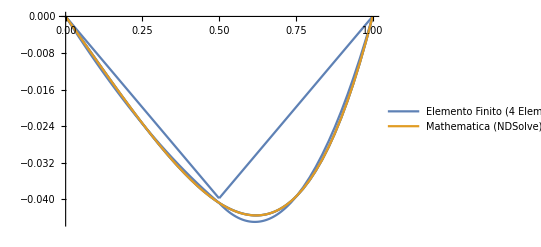

```mathematica
f=y[x]/.DSolve[{-y''[x]-y[x]==-x^2,y[0]==0,y[1]==0},y[x],x];
Plot[{u,f(1.),Abs[u-f(1.)]},{x,0,1},PlotLegends->{"Elemento Finito (4 Elementos)", "Mathematica (NDSolve)", "Error"}]
```

```mathematica
u=Table[ElementoFinitoDirichlet1D[-x^2,i,2,{0,1},Bilineal2,0],{i,4}];
```

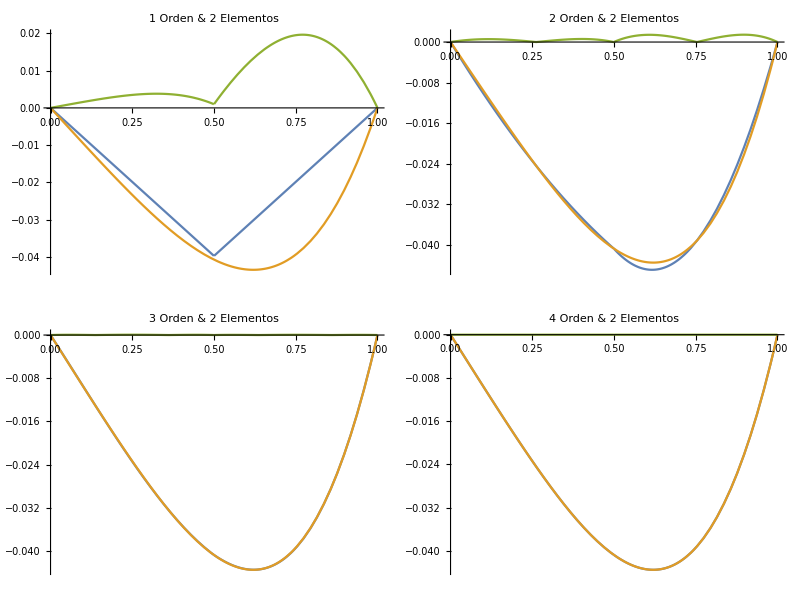
(-Graphics-)

```mathematica
MatrixForm[Partition[Table[Plot[{u[[i]],f,Abs[u[[i]]-f]},{x,0,1},PlotLabel->ToString[i]<>" Orden & 2 Elementos"],{i,4}],2]]
```